## Making the simulation

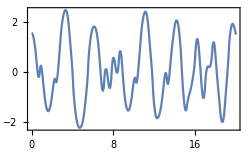
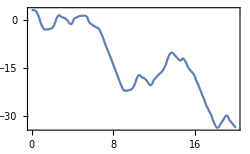

```mathematica
ke=1/2 Subscript[m, 1](Subscript[L, 1] θ'[t])^2+1/2 Subscript[m, 2]((Subscript[L, 2] (ϕ'[t])+Subscript[L, 1] θ'[t] Cos[ϕ[t]-θ[t]])^2+(Subscript[L, 1] θ'[t] Sin[ϕ[t]-θ[t]])^2); (*Kinetic Energy*)
pe=-Subscript[L, 1] Subscript[m, 1] g Cos[θ[t]]-(Subscript[L, 1] Cos[θ[t]]+Subscript[L, 2] Cos[ϕ[t]]) Subscript[m, 2] g; (*Potential Energy*)

eq1=D[D[ke-pe,θ'[t]],t]-D[ke-pe,θ[t]]; (*Equation for motion of θ*)
sol1=First@Solve[eq1==0,θ''[t]];

eq2=D[D[ke-pe,ϕ'[t]],t]-D[ke-pe,ϕ[t]]; (*Equation for motion of ϕ*)
sol1=First@Solve[eq2==0,ϕ''[t]];

sol=First@Solve[{eq1==0,eq2==0},{θ''[t],ϕ''[t]}]; (*Decouple the two equations above*)

pars={Subscript[L, 1]->1,Subscript[L, 2]->1,Subscript[m, 1]->1,Subscript[m, 2]->1,g->9.8}; (*Parameters of double pendulum*)
ic={θ[0]==π/2,θ'[0]==0,ϕ[0]==(2 π)/2,ϕ'[0]==0}; (*Initial conditions*)
dur=20; (*simDuration*)
numericalSolution=First@NDSolve[Flatten[{eq1==0,eq2==0,ic}]/.pars,{θ[t],ϕ[t]},{t,0,dur}]; (*Numerical solution for θ(t) and ϕ(t)*)

θn[t_]:=Evaluate[θ[t]/.numericalSolution];
Subscript[x, 1][t_]:=Values[pars][[1]]*Sin[θn[t]]
Subscript[y, 1][t_]:=-Values[pars][[1]]*Cos[θn[t]]

ϕn[t_]:=Evaluate[ϕ[t]/.numericalSolution];
Subscript[x, 2][t_]:=Values[pars][[1]]*Sin[θn[t]]+Values[pars][[2]]*Sin[ϕn[t]]
Subscript[y, 2][t_]:=-Values[pars][[1]]*Cos[θn[t]]-Values[pars][[2]]*Cos[ϕn[t]]

Row[{
Plot[θ[t]/.numericalSolution,{t,0,dur},Frame->True,ImageSize->250,FrameLabel->{{None,None},{"t","θ(t)"}}],
Plot[ϕ[t]/.numericalSolution,{t,0,dur},Frame->True,ImageSize->250,FrameLabel->{{None,None},{"t","ϕ(t)"}}]
}]
Manipulate[Show[{
ParametricPlot[{Subscript[x, 1][t],Subscript[y, 1][t]},{t,0,tf},PlotRange->1.05 {{-2,2},{-2,2}},PlotStyle->{Red,Thickness->0.001}],
Graphics[{Red,Thickness->0.005,Line[{{0,0},{Subscript[x, 1][tf],Subscript[y, 1][tf]}}]}],
Graphics[{PointSize->0.015,Red,Point[{Subscript[x, 1][tf],Subscript[y, 1][tf]}]}],

ParametricPlot[{Subscript[x, 2][t],Subscript[y, 2][t]},{t,0,tf},PlotStyle->{Blue,Thickness->0.001}],
Graphics[{Blue,Thickness->0.005,Line[{{Subscript[x, 1][tf],Subscript[y, 1][tf]},{Subscript[x, 2][tf],Subscript[y, 2][tf]}}]}],
Graphics[{PointSize->0.015,Blue,Point[{Subscript[x, 2][tf],Subscript[y, 2][tf]}]}]
}]
,{tf,0.01,dur,0.01}]
```

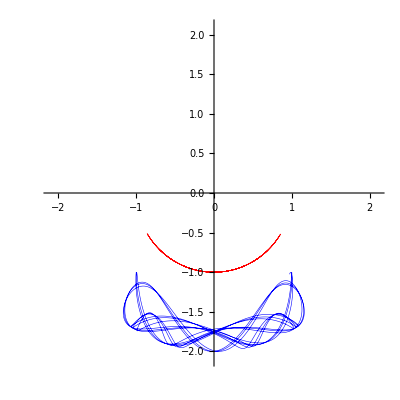

```mathematica
Show[{
ParametricPlot[{Subscript[x, 1][t],Subscript[y, 1][t]},{t,0,dur},PlotRange->1.05 {{-2,2},{-2,2}},PlotStyle->{Red,Thickness->0.001}],
ParametricPlot[{Subscript[x, 2][t],Subscript[y, 2][t]},{t,0,dur},PlotStyle->{Blue,Thickness->0.001}]
}]
```

## Collecting Data

```mathematica
Import[StringJoin[NotebookDirectory[],"dataCollect.mx"]]
```

```mathematica
ke=1/2 Subscript[m, 1](Subscript[L, 1] θ'[t])^2+1/2 Subscript[m, 2]((Subscript[L, 2] (ϕ'[t])+Subscript[L, 1] θ'[t] Cos[ϕ[t]-θ[t]])^2+(Subscript[L, 1] θ'[t] Sin[ϕ[t]-θ[t]])^2); (*Kinetic Energy*)
pe=-Subscript[L, 1] Subscript[m, 1] g Cos[θ[t]]-(Subscript[L, 1] Cos[θ[t]]+Subscript[L, 2] Cos[ϕ[t]]) Subscript[m, 2] g; (*Potential Energy*)

eq1=D[D[ke-pe,θ'[t]],t]-D[ke-pe,θ[t]]; (*Equation for motion of θ*)
sol1=First@Solve[eq1==0,θ''[t]];

eq2=D[D[ke-pe,ϕ'[t]],t]-D[ke-pe,ϕ[t]]; (*Equation for motion of ϕ*)
sol1=First@Solve[eq2==0,ϕ''[t]];

sol=First@Solve[{eq1==0,eq2==0},{θ''[t],ϕ''[t]}]; (*Decouple the two equations above*)

pars={Subscript[L, 1]->1,Subscript[L, 2]->1,Subscript[m, 1]->1,Subscript[m, 2]->1,g->9.8}; (*Parameters of double pendulum*)
dur=20; (*simDuration*)

dataCollect={};
Timing[
 Table[{
ic={θ[0]==a,θ'[0]==0,ϕ[0]==b,ϕ'[0]==0}; (*Initial conditions*)
numericalSolution=First@NDSolve[Flatten[{eq1==0,eq2==0,ic}]/.pars,{θ[t],ϕ[t]},{t,0,dur}]; (*Numerical solution for θ(t) and ϕ(t)*)

θn[t_]:=Evaluate[θ[t]/.numericalSolution];
Subscript[x, 1][t_]:=Values[pars][[1]]*Sin[θn[t]];
Subscript[y, 1][t_]:=-Values[pars][[1]]*Cos[θn[t]];

ϕn[t_]:=Evaluate[ϕ[t]/.numericalSolution];
Subscript[x, 2][t_]:=Values[pars][[1]]*Sin[θn[t]]+Values[pars][[2]]*Sin[ϕn[t]];
Subscript[y, 2][t_]:=-Values[pars][[1]]*Cos[θn[t]]-Values[pars][[2]]*Cos[ϕn[t]];



AppendTo[dataCollect,{a,b,θ[t]/.numericalSolution,
ϕ[t]/.numericalSolution}];

},{a,0,π,π/90},{b,0,2 π,π/90}];
]
```

{796.047,Null}

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"dataCollect.mx"}],dataCollect];
```

```mathematica
Dimensions[dataCollect]
```

{16471,4}

{0,0,InterpolatingFunction[{{0., 20.}}, <>][t],InterpolatingFunction[{{0., 20.}}, <>][t]}

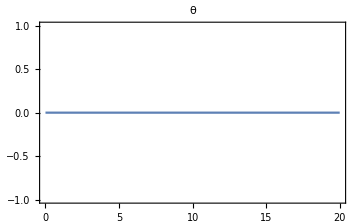
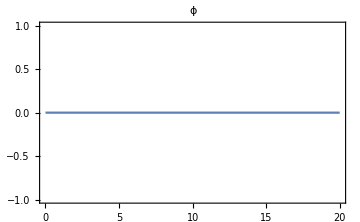

```mathematica
dataCollect[[1]]
Row[{Plot[%[[-2]],{t,0,dur},ImageSize->Medium,Frame->True,PlotLabel->"θ"],
Plot[%[[-1]],{t,0,dur},ImageSize->Medium,Frame->True,PlotLabel->"ϕ"]}]
```